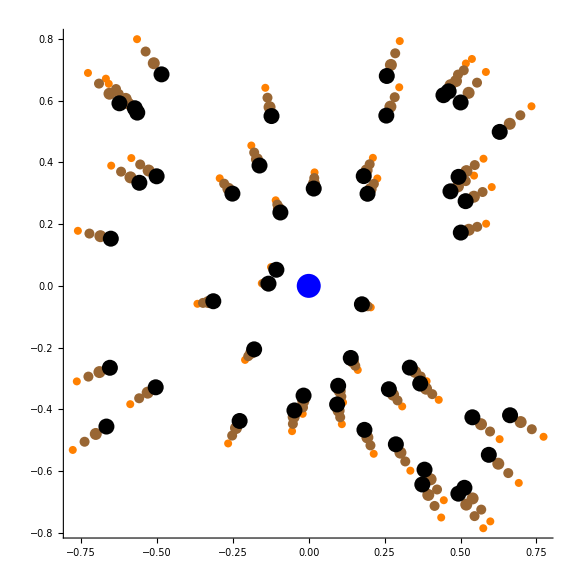

```mathematica
(* Enemy avoidance demonstration *)
ClearAll["Global`*"];
n=50; (* Number of points *)
mapSize=0.8;
dim=2;
x=RandomReal[{-mapSize,mapSize},{n,dim}]; (* Random creature points *)

leaderCoordinates = ConstantArray[0,dim]; (* Centered start point *)

(* Vector Distance *)
vecXL:=-x+ConstantArray[leaderCoordinates[[]],{n}];

(* Euclidean Distance *)
magXL:=0.5*Outer[EuclideanDistance,leaderCoordinates,x,1];

(* Standardised Move direction *)(* {1,1,1} cube *)
dirXL:=Outer[Normalize,vecXL,1];

(* Movement vector corresponding to a move away from the hunter for each creature. *)
movXL:=dirXL*magXL[[1]]/10;

Framed[
Show[{
Graphics[{PointSize[0.03],Blue,Point[leaderCoordinates]},ImageSize->Large,If[dim==3,SphericalRegion->True];PlotRange->1.25*mapSize,Axes->True
]},
x=x;(* For neatness *)
{
Graphics[{PointSize[0.01],Orange,Point[x]}
]},
x=x+movXL; (* Advance creatures by one move relative to hunter. *)
{
Graphics[{PointSize[0.0125],Brown,Point[x]}
]},
x=x+movXL; (* Advance creatures by one move relative to hunter. *)
{
Graphics[{PointSize[0.015],Brown,Point[x]}
]},
x=x+movXL; (* Advance creatures by one move relative to hunter. *)
{
Graphics[{PointSize[0.02],Black,Point[x]}
]}
]]
```

```mathematica
(* Enemy avoidance demonstration *)
n=50; (* Number of points *)
mapSize=0.8;
dim=3;

hunterCoordinates = ConstantArray[0,3]; (* Centered start point *)
x=RandomReal[{-mapSize,mapSize},{n,3}]; (* Random creature points *)

(* Vector Distance *)
vecXH:=-x+ConstantArray[hunterCoordinates[[]],{n}]

(* Euclidean Distance *)
magXH:=Outer[EuclideanDistance,hunterCoordinates,x,1]

(* Standardised Move direction *)(* {1,1,1} cube *)
dirXH:=Outer[Normalize,vecXH,1]

(* Movement vector corresponding to a move away from the hunter for each creature. *)
movXH:=dirXH/(25*magXH[[1]])

Framed[
Show[{
Graphics3D[{PointSize[0.03],Red,Point[hunterCoordinates]},ImageSize->Large,SphericalRegion->True,PlotRange->1.25*mapSize,Axes->True
]},
x=x; (* For neatness sake. *)
{
Graphics3D[{PointSize[0.01],Orange,Point[x]}
]},
x=x-movXH; (* Advance creatures by one move relative to hunter. *)
{
Graphics3D[{PointSize[0.0125],Brown,Point[x]}
]},
x=x-movXH; (* Advance creatures by one move relative to hunter. *)
{
Graphics3D[{PointSize[0.015],Brown,Point[x]}
]},
x=x-movXH; (* Advance creatures by one move relative to hunter. *)
{
Graphics3D[{PointSize[0.02],Black,Point[x]}
]}
]]
```

-Graphics3D-

```mathematica
leaderCoordinates=ConstantArray[0,dim]; (* Centered start point *)
hunterCoordinates=ConstantArray[1,dim];

Framed[
Show[{
Graphics3D[{PointSize[0.03],Red,Point[hunterCoordinates]},ImageSize->Large,SphericalRegion->True,PlotRange->1.25*mapSize,Axes->True
]},
{
Graphics3D[{PointSize[0.03],Blue,Point[leaderCoordinates]}
]},
x=x; (* For neatness sake. *)
{
Graphics3D[{PointSize[0.01],Orange,Point[x]}
]},
x=x+movXL;
x=x-movXH; (* Advance creatures by one move relative to hunter. *)
{
Graphics3D[{PointSize[0.0125],Brown,Point[x]}
]},
x=x+movXL;
x=x-movXH; (* Advance creatures by one move relative to hunter. *)
{
Graphics3D[{PointSize[0.015],Brown,Point[x]}
]},
x=x+movXL;
x=x-movXH; (* Advance creatures by one move relative to hunter. *)
{
Graphics3D[{PointSize[0.02],Black,Point[x]}
]}
]]
```

-Graphics3D-

```mathematica
(* ---------- Setup variables ---------- *)

Clear["Global`*"]

n=250; (* Number of entities *)
mapSize=1.5; (* Total map size *)
dim=2; (* To switch between 2D/3D, change Graphics3D to Graphics in the dynamic loop (At the bottom), and this value between 2/3 *)

leaderCircleDepth = 1.0;(* Depth of ellipse followed by leader *)
leaderCircleWidth=1.0; (* Width of ellipse followed by leader *)
leaderCircleHeight = 1.0; (* Height of ellipse followed by leader *)
leaderSpeed=1; (* Speed of leader *)
leaderCoordinates =ConstantArray[1,dim];(* Starting leader coordinates *)
leaderCount=0.0; (* Leader staring angle *) (* Only works with ellipse *)

hunterCircleDepth = 1.8;(* Depth of ellipse followed by hunter *)
hunterCircleWidth = 0.9; (* Width of ellipse followed by hunter *)
hunterCircleHeight=0.0; (* Height of ellipse followed by hunter *)
hunterSpeed = 1.5; (* Speed of hunter *)
hunterCoordinates = ConstantArray[-1,dim];(* Starting hunter coordinates *)
hunterCount=Pi/2; (* Hunter staring angle *) (* Only works with ellipse *)

(* ---------- Fixed calculations ---------- *)

leaderSpeedAngular=leaderSpeed/(((leaderCircleDepth+leaderCircleWidth)/4)*Pi); (* Converts leader speed to angular speed *)
hunterSpeedAngular=hunterSpeed/(((hunterCircleDepth+hunterCircleWidth)/4)*Pi); (* Converts hunter speed to angular speed *)

x=RandomReal[{-mapSize,mapSize},{n,dim}]; (* Establishes initial creature coordinates *)

{p,q}=RandomInteger[{1,n},{2,n}]; (* p and q are random entities at initialisation representing friends and enemies *)

(* ---------- Functions ---------- *)

r:=RandomInteger[{1,n}]; (* r is a function that returns a random entity *)

f:=(#/(.01+Sqrt[Dot[#,#]]))&/@ (* Divide each vector (from next line) by (.01 + it's length) *)
(x[[#]]-x)&; (* An array of vectors from every point to a selected point *)
(* The function f returns an array of vectors. These vectors point from every entity towards a specified entity. The magnitude of these vectors is slightly less than that of a unit vector, and tends to zero as the distance between entities gets smaller *)

(* Vector Distance *)
vecXL:=-x+ConstantArray[leaderCoordinates[[]],{n}](* Calculates vector distance between each boid and leader *)
vecXH:=-x+ConstantArray[hunterCoordinates[[]],{n}](* Calculates vector distance between each boid and hunter *)

(* Euclidean Distance *)
magXL:=
0.9*Outer[EuclideanDistance,leaderCoordinates,x,1](* Calculates Euclidean distance between each boid and leader *)
magXH:=0.9*Outer[EuclideanDistance,hunterCoordinates,x,1](* Calculates Euclidean distance between each boid and hunter    *)

(* Standardised Move direction *)(* {1,1,1} cube *)
dirXL:=Outer[Normalize,vecXL,1]
dirXH:=Outer[Normalize,vecXH,1]

(* Movement vector corresponding to a move away from the hunter for each creature. *)
movXL:=dirXL*magXL[[1]]/100
movXH:=dirXH/(100*magXH[[1]])

s:=With[{r1=r},p[[r1]]=r;q[[r1]]=r];(* for a random entity (the same random element in the p and q lists), s is a function to pick a new "friend" p and "enemy" q *)

(* ---------- Checking for errors ---------- *)

If[Max[leaderCircleHeight,leaderCircleWidth]>mapSize,Print["Leader is circling outside of map!"]];
If[Max[hunterCircleHeight,hunterCircleWidth]>mapSize,Print["Hunter is circling outside of map!"]];
```

```mathematica
(* This is the Dynamically run code section *)
Framed[
Graphics[ (* <<<--------- Change this to switch between 2D/3D *)
{
PointSize[0.015],Blue,Dynamic[  (* Updates leader position *)
If[leaderCount>2*Pi,leaderCount=0,leaderCount=leaderCount+leaderSpeedAngular*0.01];
leaderCoordinates[[1]]=leaderCircleWidth*Cos[leaderCount];
leaderCoordinates[[2]]=leaderCircleDepth*Sin[leaderCount];
If[dim==3,leaderCoordinates[[3]]=leaderCircleHeight*Cos[leaderCount]];
Point[leaderCoordinates]
],
PointSize[0.015],Red,Dynamic[  (* Updates hunter position *)
If[hunterCount>2*Pi,hunterCount= 0,hunterCount=hunterCount+hunterSpeedAngular*0.01];
hunterCoordinates[[1]]=hunterCircleWidth*Sin[hunterCount];
hunterCoordinates[[2]]=hunterCircleDepth*Cos[hunterCount];
If[dim==3,hunterCoordinates[[3]]=hunterCircleHeight*Cos[hunterCount]];
Point[hunterCoordinates]
],
PointSize[0.005],Black,Dynamic[ (* Updates following animals *)
If[r<(n/20),s];(* If a randomly chosen entity has ID < 100 (10% chance), run s *)
x=x+0.038*f[p];(* Move closer to "friend" p *)
x=x+1.0*movXL; (* Move closer to "leader" fl *)
x=x-0.04f[q];(* Move away from "enemy" q *)
x=x-0.5movXH;(* Move away from hunter *)
Point[x]
]
},
PlotRange->2.0*mapSize,
If[dim==3,SphericalRegion->True];
ImageSize->Large
]]
```

-Graphics-